# Solution for Problem 2 by Max-Cut

## Author

Pei-Xin Shen
Last update May 14 , 2019
For more information, please contact shenpx17@mails.tsinghua.edu.cn.
Acknowledgement: Yu Shi, Wen-Jie Jiang and Tie-Cheng Guo.

## Plots

3D

```mathematica
PolyhedronData["TruncatedIcosahedron","Edges"];
Graph3D[UndirectedEdge@@@%]
```

-Graphics3D-

2D

```mathematica
GraphData["TruncatedIcosahedralGraph",{"EdgeCount","FaceCount","VertexCount"}]
```

{90,32,60}

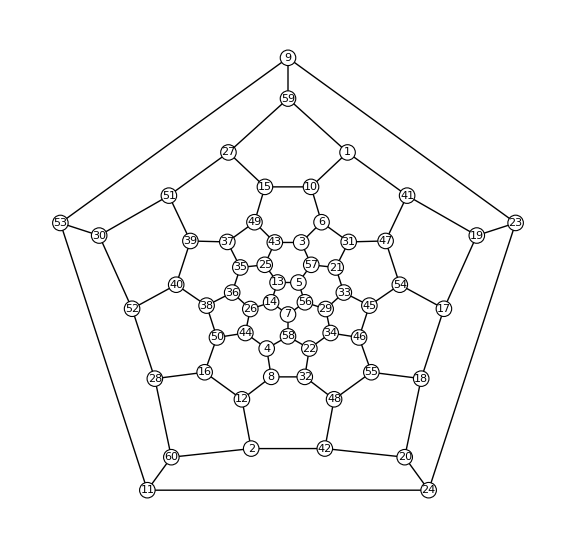

```mathematica
GraphPlot[GraphData["TruncatedIcosahedralGraph"],VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.2],Black,Text[#2,#1]}&),PlotStyle->{Black},ImageSize->Large]
```

## Graph Theory

Corresponding to a Max-Cut Problem in Graph Theory

-Graphics-

Max-Cut of Planar Graph Can be Solved in Polynomial Time

The problem of finding a maximum cut of an arbitrary graph is one of a list of 21 combinatorial problems (Karp-Cook list). It is unknown whether or not there exist algorithms operating in polynomial bounded time for any of these problems. It has been shown that existence for one implies existence for all. In this paper we deal with a special case of the maximum cut problem. By requiring the graph to be planar, it is shown the problem can be translated into a maximum weighted matching problem for which there exists a polynomial bounded algorithm.
(FINDING A MAXIMUM CUT OF A PLANAR GRAPHIN POLYNOMIAL TIME F. HADLOCK, SIAM J. CoMPtrr. Vol. 4, No. 3, September 1975)

## Algorithm

Transformed to Dual

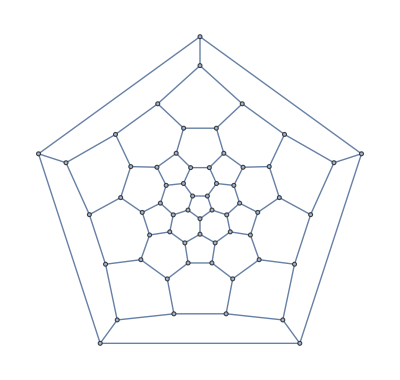
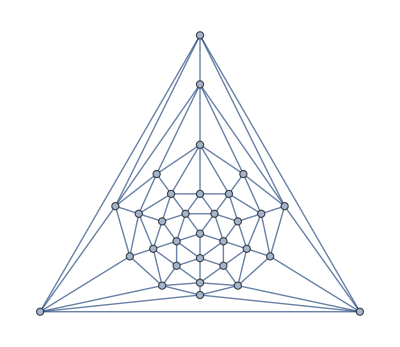

```mathematica
{g0=GraphData["TruncatedIcosahedralGraph"],g1=GraphData["TruncatedIcosahedralGraph","DualGraph"]}
```

Ground Energy

Note: I made a mistake in my presentation when explaining the factor of -90, it should be an ideal case of up-down pairing of spins

```mathematica
VertexDegree[g1]
r=Count[%,_?OddQ]
-90+2r
```

{5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,6,6,6,6,5,5,5,5,6}

12

-66

Degeneracy

Merging those pentagon into a 12 points, A minimum odd-circuit cover may be found by determining a minimum odd pairing of the geometric dual.

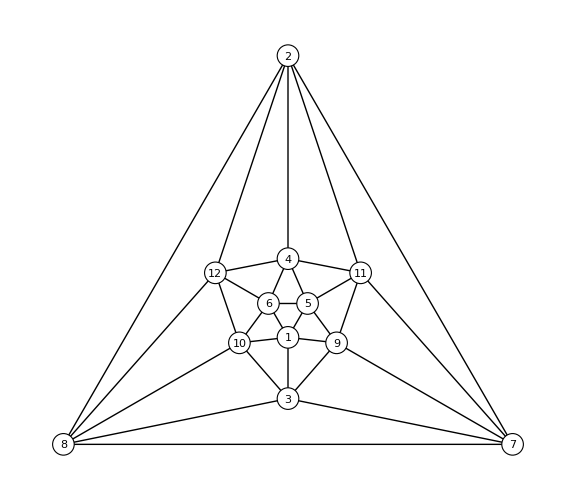

```mathematica
GraphPlot[g3=GraphData["IcosahedralGraph"],VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.15],Black,Text[#2,#1]}&),PlotStyle->{Black},ImageSize->Large]
```

```mathematica
edgelist=EdgeList[g3]/.{x_<->y_:>{x,y}}
matchlist=Cases[Subsets[edgelist,{6}],{A__}/;DuplicateFreeQ@Flatten@{A}];
Length@matchlist(*in this version, we don't need python to solve out 125 anymore*)
```

{{1,3},{1,5},{1,6},{1,9},{1,10},{2,4},{2,7},{2,8},{2,11},{2,12},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,11},{4,12},{5,6},{5,9},{5,11},{6,10},{6,12},{7,8},{7,9},{7,11},{8,10},{8,12},{9,11},{10,12}}

125

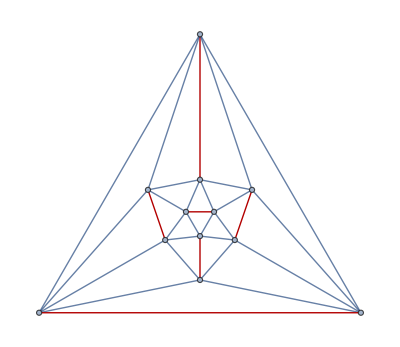
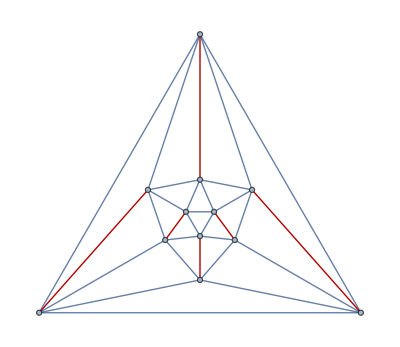
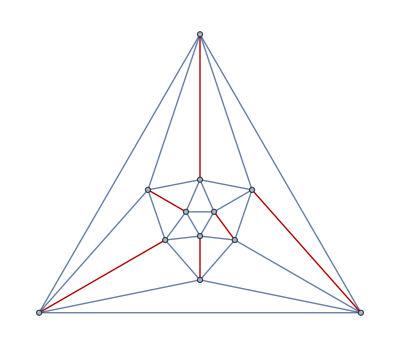
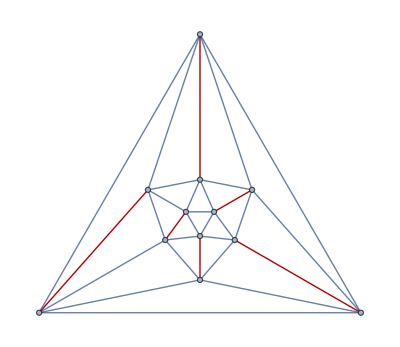
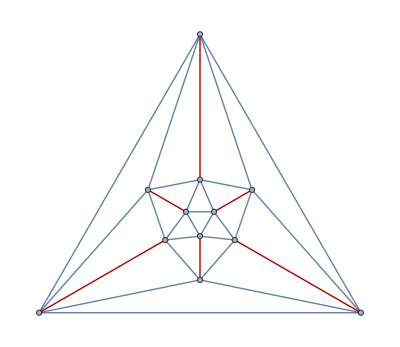

```mathematica
Table[HighlightGraph[g3,matchlist[[i]]/.{{x_,y_}:>x<->y}],{i,1,5}](*plotting the first-five matches for check*)
```

Considering the trivial symmetries of the system, we obtain the degeneracy

```mathematica
2(*Subscript[Z, 2] symmetry*)*125(*number of matchlist*)*2^6(*cutting 2 edges in original pentagon*)
```

16000

# Appendix

These two examples are just solved by brute-force enumeration for fun :)

## Toy Model

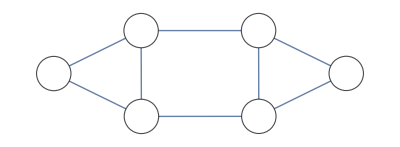
```mathematica
g = -Graphics-;
allcases=Tuples[{-1,1},6];
edgelist=EdgeList[g]/.{x_<->y_:>{x,y}};
allcut=Table[Total[Times@@allcases[[k]][[#1]]&/@edgelist],{k,2^6}];
maxcut=Min@allcut
numbercut=Count[allcut,maxcut]
Flatten@Position[allcut,maxcut];
casecut=allcases[[%]]
Table[HighlightGraph[g,Map[Subgraph[g,#]&,Flatten@Position[casecut[[i]],#]&/@{1,-1}]],{i,1,numbercut}]
```

-4

10

{{-1,-1,1,-1,1,-1},{-1,-1,1,1,1,-1},{-1,1,-1,-1,-1,1},{-1,1,-1,1,-1,1},{-1,1,-1,1,1,-1},{1,-1,1,-1,-1,1},{1,-1,1,-1,1,-1},{1,-1,1,1,1,-1},{1,1,-1,-1,-1,1},{1,1,-1,1,-1,1}}

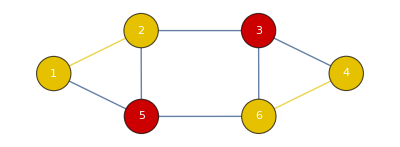
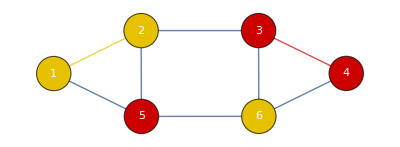
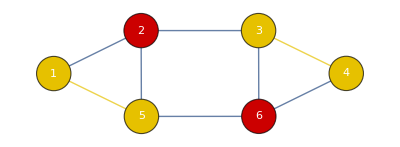
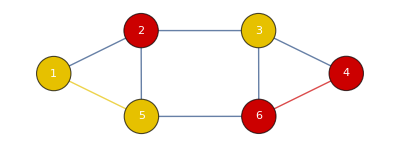
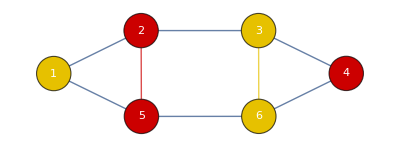
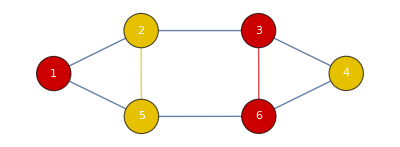
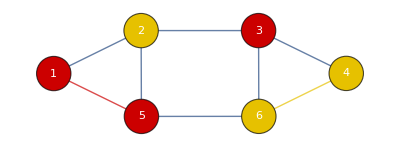
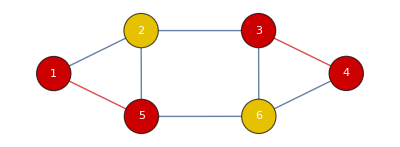

## Complicated Graph

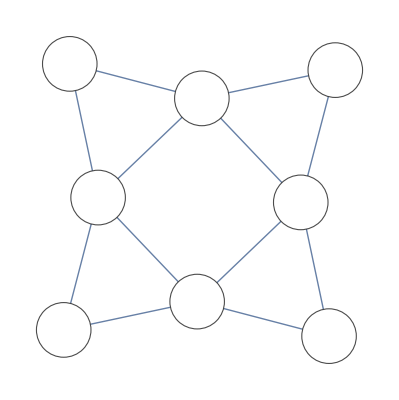
```mathematica
g = -Graphics-;
allcases=Tuples[{-1,1},8];
edgelist=EdgeList[g]/.{x_<->y_:>{x,y}};
allcut=Table[Total[Times@@allcases[[k]][[#1]]&/@edgelist],{k,2^8}];
maxcut=Min@allcut
numbercut=Count[allcut,maxcut]
Flatten@Position[allcut,maxcut];
casecut=allcases[[%]];
Table[HighlightGraph[g,Map[Subgraph[g,#]&,Flatten@Position[casecut[[i]],#]&/@{1,-1}]],{i,1,numbercut}]
```

-4

82